# Efficiency Comparison Physics Data

## Defining Methods and Preamble

## Preamble

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
```

## Plotting Method

```mathematica
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
RGBColor/@hexColors
makeBoxCMS[data_,labels_,yLabel_,cmsPos_,tevPos_,precY_:1,xLabelY_:0.06,modelLabel_:"AE", modelLabelPos_:{0.639,0.899}]:=Module[{majorLen,minorLen,makeTicks01,yVals,yTicks,yTicksRight,plot,cmsText,tevText,plotLeft=0.01,plotBottom=0.12,plotWidth=0.98,plotHeight=0.84,xCenters},majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
makeTicks01[{vmin_?NumericQ,vmax_?NumericQ},prec_]:=Module[{maj,min},maj=N@FindDivisions[{vmin,vmax},6];
min=N@Flatten@Table[Most@Rest@Subdivide[maj[[k]],maj[[k+1]],6],{k,1,Length[maj]-1}];
Join[({#,NumberForm[#,{6,prec}],{majorLen,0}}&/@maj),({#,"",{minorLen,0}}&/@min)]];
yVals=Flatten[data];
yTicks=makeTicks01[{0,1.05 Max[yVals]},precY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};


nBoxes=Length[data];
q10=Quantile[#,0.10]&/@data;
q90=Quantile[#,0.90]&/@data;
(*x positions in BoxWhiskerChart coordinates*)
xPos=Range[nBoxes];
     p10p90Graphics=Table[{EdgeForm[None],FaceForm[Directive[RGBColor["#92dadd"],Opacity[0.22]]],Rectangle[{xPos[[i]]-0.39,q10[[i]]},{xPos[[i]]+0.39,q90[[i]]}]},{i,nBoxes}];

plot=BoxWhiskerChart[
data,
{"Outliers",
{"MedianMarker",1.0,Directive[RGBColor["#94a4a2"],AbsoluteThickness[3], Opacity[2]]},
{"Whiskers",Directive[Black,AbsoluteThickness[3]]},
{"Fences",0.5,Directive[Black,AbsoluteThickness[2]]},
{"MeanMarker",0.78,Directive[Black, Opacity[1],AbsoluteThickness[3]]},
{"MeanDiamond",0.8,Directive[RGBColor["#92dadd"], Opacity[0.4]]},
{"Outliers",Graphics[{RGBColor["#3f90da"],Rectangle[{-1,-1},{1,1}]}]}
},
Prolog->p10p90Graphics,
BarSpacing->0.3,
ChartStyle->Table[Directive[RGBColor["#3f90da"],Opacity[0.8]],{Length[data]}],
Frame->True,Axes->False,
FrameTicks->{{yTicks,yTicksRight},{Automatic,Automatic}},
FrameStyle->Directive[Black,AbsoluteThickness[2]],
FrameTicksStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"],
LabelStyle->Directive[Black,FontSize->24,FontFamily->"TeX Gyre Heros"],
FrameLabel->{None,Style[yLabel,Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},
GridLines->{None,Automatic},GridLinesStyle->Directive[GrayLevel[0.85], AbsoluteThickness[1.5]],
ImageSize->1300,AspectRatio->0.65,ImagePadding->{{100,40},{40,40}},PlotRange->{0,1.05 Max[yVals]},
PlotRangePadding->{{Scaled[-0.1],Scaled[-0.03]},{Scaled[0.03],Scaled[0.01]}}
];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText=Style["14 TeV",FontFamily->"TeX Gyre Heros",24];
xCenters={0.165, 0.3,0.43, 0.57};

Graphics[
Join[
{
Inset[plot,Scaled[{plotLeft,plotBottom}],{Left,Bottom},Scaled[{plotWidth,plotHeight}]]},
Table[Inset[Style[labels[[i]],FontFamily->"TeX Gyre Heros",22],Scaled[{xCenters[[i]],xLabelY}],{Center,Top}],{i,Length[labels]}],
{
Inset[cmsText,Scaled[cmsPos],{Left,Bottom}],
Inset[tevText,Scaled[tevPos],{Right,Bottom}],
Inset[Framed[Style[modelLabel,FontFamily->"TeX Gyre Heros",Italic,32,Black],Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],RoundingRadius->0,FrameMargins->{{8,8},{4,4}}],Scaled[modelLabelPos],{Right,Top}]
}],PlotRange->{{0,1},{0,1}},AspectRatio->0.5,ImageSize->1300]]
```

{RGBColor[0.24705882352941178, 0.5647058823529412, 0.8549019607843137],RGBColor[1., 0.6627450980392157, 0.054901960784313725],RGBColor[0.7411764705882353, 0.12156862745098039, 0.00392156862745098],RGBColor[0.5803921568627451, 0.6431372549019608, 0.6352941176470588],RGBColor[0.5137254901960784, 0.17647058823529413, 0.7137254901960784],RGBColor[0.6627450980392157, 0.4196078431372549, 0.34901960784313724],RGBColor[0.9058823529411765, 0.38823529411764707, 0.],RGBColor[0.7254901960784313, 0.6745098039215687, 0.4392156862745098],RGBColor[0.44313725490196076, 0.4588235294117647, 0.5058823529411764],RGBColor[0.5725490196078431, 0.8549019607843137, 0.8666666666666667]}

```mathematica
ClearAll[BootstrapPairedDiffCI,WilcoxonSignedRankPExact,SafeWilcoxonP,CollapsedMethodQ,FormatNum,FormatP,FormatMeanOrDash,FormatAsymPMOrDash,ArchitectureRowDataCompactCollapse,LatexRowCompactAsymCollapse,BuildArchitectureRowsCompactCollapse,BuildLatexTableCompactAsymCollapse];

(*Treat all-zero arrays as collapsed*)
CollapsedMethodQ[x_List]:=AllTrue[x,#==0.&];

(*95% bootstrap CI for paired mean difference:a-b*)
BootstrapPairedDiffCI[a_List,b_List,nBoot_:10000,alpha_:0.05]:=Module[{n,diffs,boots},If[Length[a]=!=Length[b],Return[Missing["LengthMismatch"]]];
n=Length[a];
diffs=a-b;
boots=Table[Mean[RandomChoice[diffs,n]],{nBoot}];
Quantile[boots,{alpha/2,1-alpha/2}]];

(*Exact two-sided Wilcoxon signed-rank p-value*)
WilcoxonSignedRankPExact[a_List,b_List]:=Module[{d,absd,sgn,n,order,sortedAbs,sortedIdx,ranks,groups,start,wPlus,allSums,pLeft,pRight},If[Length[a]=!=Length[b],Return[Missing["LengthMismatch"]]];
d=DeleteCases[a-b,0.];
If[d==={},Return[1.0]];
absd=Abs[d];
sgn=Sign[d];
n=Length[d];
order=Ordering[absd];
sortedAbs=absd[[order]];
sortedIdx=order;
ranks=ConstantArray[0.,n];
groups=Split[Range[n],sortedAbs[[#1]]==sortedAbs[[#2]]&];
start=1;
Do[Module[{len=Length[g],mid},mid=Mean[Range[start,start+len-1]];
ranks[[sortedIdx[[g]]]]=mid;
start+=len;],{g,groups}];
wPlus=Total[Pick[ranks,sgn,1]];
allSums=Total/@(Pick[ranks,#,1]&/@Tuples[{0,1},n]);
pLeft=N[Count[allSums,x_/;x<=wPlus]/Length[allSums]];
pRight=N[Count[allSums,x_/;x>=wPlus]/Length[allSums]];
Min[1.0,2.0 Min[pLeft,pRight]]];

SafeWilcoxonP[a_List,b_List]:=WilcoxonSignedRankPExact[a,b];

FormatNum[x_,digits_:2]:=ToString@NumberForm[x,{Infinity,digits},NumberPadding->{"","0"},NumberPoint->"."];

FormatP[p_]:=Which[MissingQ[p],"-",p<0.001,"<0.001",True,ToString@NumberForm[p,{Infinity,3},NumberPadding->{"","0"},NumberPoint->"."]];

FormatMeanOrDash[x_List,digits_:2]:=If[CollapsedMethodQ[x],"-",FormatNum[Mean[x],digits]];

FormatAsymPMOrDash[center_,ci_List,digits_:2]:=Module[{lower,upper},If[MissingQ[center]||MissingQ[ci],Return["-"]];
lower=center-ci[[1]];
upper=ci[[2]]-center;
"$"<>FormatNum[center,digits]<>"^{+"<>FormatNum[upper,digits]<>"}"<>"_{-"<>FormatNum[lower,digits]<>"}$"];

ArchitectureRowDataCompactCollapse[archName_String,methods_Association,nBoot_:10000,alpha_:0.05]:=Module[{semi,cap,stable,w1,semiCollapsed,capCollapsed,stableCollapsed,w1Collapsed,dCS,dCW,ciCS,ciCW,pCS,pCW},semi=methods["semisupervised"];
cap=methods["CAP"];
stable=methods["stable"];
w1=methods["wasserstein"];
If[!(Length[semi]==Length[cap]==Length[stable]==Length[w1]),Return[<|"Architecture"->archName,"Error"->"All method arrays must have equal lengths."|>]];
semiCollapsed=CollapsedMethodQ[semi];
capCollapsed=CollapsedMethodQ[cap];
stableCollapsed=CollapsedMethodQ[stable];
w1Collapsed=CollapsedMethodQ[w1];
dCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],Mean[cap-stable]];
dCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],Mean[cap-w1]];
ciCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],BootstrapPairedDiffCI[cap,stable,nBoot,alpha]];
ciCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],BootstrapPairedDiffCI[cap,w1,nBoot,alpha]];
pCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],SafeWilcoxonP[cap,stable]];
pCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],SafeWilcoxonP[cap,w1]];
<|"Architecture"->archName,"Semi"->semi,"CAP"->cap,"Stable"->stable,"W1"->w1,"CAPMinusStable"->dCS,"CAPMinusStableCI"->ciCS,"CAPMinusStableP"->pCS,"CAPMinusW1"->dCW,"CAPMinusW1CI"->ciCW,"CAPMinusW1P"->pCW|>];

LatexRowCompactAsymCollapse[row_Association,digits_:2]:=StringRiffle[{row["Architecture"],FormatMeanOrDash[row["Semi"],digits],FormatMeanOrDash[row["CAP"],digits],FormatMeanOrDash[row["Stable"],digits],FormatMeanOrDash[row["W1"],digits],FormatAsymPMOrDash[row["CAPMinusStable"],row["CAPMinusStableCI"],digits],FormatP[row["CAPMinusStableP"]],FormatAsymPMOrDash[row["CAPMinusW1"],row["CAPMinusW1CI"],digits],FormatP[row["CAPMinusW1P"]]}," & "]<>" \\\\";

BuildArchitectureRowsCompactCollapse[allArchitectures_Association,nBoot_:10000,alpha_:0.05]:=KeyValueMap[ArchitectureRowDataCompactCollapse[#1,#2,nBoot,alpha]&,allArchitectures];

BuildLatexTableCompactAsymCollapse[allArchitectures_Association,nBoot_:10000,alpha_:0.05,digits_:2]:=Module[{rows,body},rows=BuildArchitectureRowsCompactCollapse[allArchitectures,nBoot,alpha];
body=StringRiffle[LatexRowCompactAsymCollapse[#,digits]&/@rows,"\n"];
StringJoin["\\begin{tabular}{lcccccccc}\n","\\toprule\n","Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n","\\midrule\n",body,"\n","\\bottomrule\n","\\end{tabular}"]];
```

```mathematica
allArchitectures250hz=<|
"AE"-><|
"semisupervised"->{0.31,0.53,0.00,0.17,1.79,1.05,0.96,17.05,17.50,21.16,1.92,0.06,16.86,15.76,15.65,7.14,0.59,0.33,0.58,17.41},
"CAP"->{0.18,0.44,0.00,0.05,0.98,0.87,0.98,13.67,14.24,18.44,0.82,0.04,14.97,13.93,12.62,3.82,0.36,0.41,1.18,16.67},
"stable"->{2.97,0.39,0.00,0.14,0.81,0.67,0.72,9.52,9.81,14.43,0.62,0.04,12.24,9.46,8.23,2.84,0.29,0.30,0.48,11.91},
"wasserstein"->{0.16,0.22,0.00,0.03,0.77,0.57,0.66,5.38,5.42,14.82,0.51,0.02,12.21,5.47,5.32,2.45,0.20,0.18,0.33,9.64}
|>,
"VAE"-><|
"semisupervised"->{0.02,0.18,0.00,0.00,0.77,0.86,1.02,8.43,8.88,18.93,0.68,0.04,12.44,10.11,9.15,2.79,0.32,0.24,0.38,15.93},
"CAP"->{0.02,0.20,0.00,0.00,0.82,0.93,1.10,8.87,9.35,19.74,0.73,0.04,12.93,10.70,9.60,2.93,0.32,0.24,0.40,16.83},
"stable"->{0.02,0.19,0.00,0.01,0.95,1.03,1.15,6.34,6.56,21.12,0.65,0.04,15.36,8.08,7.14,2.34,0.33,0.21,0.36,15.90},
"wasserstein"->{0.02,0.21,0.00,0.01,0.91,1.07,1.17,5.77,5.92,23.70,0.78,0.04,15.10,7.62,6.77,2.76,0.32,0.12,0.18,17.37}
|>,
"DSAE"-><|
"semisupervised"->{0.47,0.59,0.00,0.10,1.22,1.04,1.16,24.23,25.34,17.00,1.16,0.05,13.27,21.69,21.13,6.43,0.40,0.60,1.00,19.04},
"CAP"->{0.39,0.61,0.00,0.10,1.23,1.08,1.20,26.20,26.86,20.58,1.12,0.05,15.23,23.61,23.15,6.91,0.43,0.68,1.12,20.36},
"stable"->{1.01,0.33,0.00,0.04,0.86,0.56,0.68,6.52,6.58,14.04,0.60,0.02,11.11,5.88,6.23,2.13,0.26,0.73,4.65,9.09},
"wasserstein"->{0.15,1.74,0.00,0.02,1.04,0.72,0.84,6.25,6.60,15.32,0.66,0.03,12.84,6.37,6.33,2.67,0.31,0.47,1.36,11.24}
|>,
"DSVAE"-><|
"semisupervised"->{0.11,0.18,0.00,0.01,1.18,0.97,1.12,12.13,12.89,17.85,0.77,0.04,14.00,13.12,11.79,3.63,0.38,0.44,0.76,16.27},
"CAP"->{0.02,0.19,0.00,0.01,1.10,1.02,1.15,9.51,10.00,19.45,0.70,0.04,15.23,11.09,9.72,3.16,0.37,0.27,0.46,16.87},
"stable"->{0.01,0.55,0.00,0.01,0.77,1.02,1.18,9.01,9.50,20.08,0.88,0.04,13.04,11.17,9.46,2.67,0.28,0.21,0.35,16.81},
"wasserstein"->{0.05,0.33,0.00,0.01,0.31,0.15,0.13,1.40,1.53,3.99,0.32,0.02,2.41,0.91,1.21,1.28,0.11,0.03,0.05,1.85}
|>,
"SVDD"-><|
"semisupervised"->{0.44,0.14,0.00,1.01,0.90,0.72,0.78,5.23,4.75,16.16,0.67,0.04,11.13,5.35,5.70,2.29,0.24,0.24,0.65,9.50},
"CAP"->{1.14,0.19,0.00,0.05,0.71,0.68,0.81,9.06,9.21,13.26,0.83,0.03,10.59,8.88,8.48,2.99,0.27,0.44,0.72,12.24},
"stable"->{0.50,0.19,0.01,0.11,1.09,0.69,0.58,8.81,8.89,8.40,1.93,0.05,8.41,7.73,7.50,6.27,0.37,0.05,0.06,9.61},
"wasserstein"->{0.71,0.09,0.00,0.03,0.55,0.46,0.58,7.57,7.98,13.30,0.38,0.02,9.92,6.44,6.05,1.91,0.20,0.09,0.14,8.63}
|>,
"RealNVP"-><|
"semisupervised"->{1.13,0.15,0.02,0.20,1.07,0.77,0.90,11.70,12.06,13.67,0.93,0.07,10.29,10.45,10.66,3.46,0.41,1.95,9.18,11.67},
"CAP"->{2.55,0.04,0.00,0.71,0.49,0.31,0.28,12.71,12.80,3.98,0.61,0.06,3.86,9.81,8.85,2.87,0.19,0.16,0.39,4.59},
"stable"->{1.47,0.04,0.00,0.17,0.34,0.36,0.37,12.19,12.77,3.79,0.54,0.04,4.60,9.92,8.83,2.26,0.14,0.15,0.23,5.09},
"wasserstein"->{0.99,0.02,0.00,0.58,0.18,0.19,0.21,6.25,6.29,1.99,0.25,0.04,2.19,5.28,4.72,1.15,0.13,0.08,0.16,2.50}
|>
|>;

compactTableTex=BuildLatexTableCompactAsymCollapse[allArchitectures250hz,10000,0.05,2];
Print[compactTableTex];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 6.84 & 5.73 & 4.29 & 3.22 & $1.44^{+0.96}_{-0.92}$ & 0.001 & $2.52^{+1.52}_{-1.37}$ & <0.001 \\
VAE & 4.56 & 4.79 & 4.39 & 4.49 & $0.40^{+0.58}_{-0.55}$ & 0.263 & $0.30^{+0.75}_{-0.74}$ & 0.659 \\
DSAE & 7.80 & 8.55 & 3.57 & 3.75 & $4.98^{+3.41}_{-3.12}$ & 0.002 & $4.80^{+3.33}_{-3.00}$ & <0.001 \\
DSVAE & 5.38 & 5.02 & 4.85 & 0.80 & $0.17^{+0.26}_{-0.20}$ & 0.172 & $4.21^{+2.50}_{-2.25}$ & <0.001 \\
SVDD & 3.30 & 4.03 & 3.56 & 3.25 & $0.47^{+0.71}_{-0.65}$ & 0.121 & $0.78^{+0.47}_{-0.39}$ & <0.001 \\
RealNVP & 5.04 & 3.26 & 3.17 & 1.66 & $0.10^{+0.17}_{-0.16}$ & 0.157 & $1.60^{+0.96}_{-0.84}$ & <0.001 \\
\bottomrule
\end{tabular}

```mathematica
allArchitecturesQ99=<|"AE"-><|"semisupervised"->{42.88,29.50,1.79,28.03,70.93,62.94,64.11,97.41,97.81,89.64,81.17,16.64,72.94,95.56,96.39,87.72,38.59,74.33,85.60,99.20},"CAP"->{39.15,17.96,2.45,24.93,63.18,60.75,62.76,97.66,97.99,89.29,80.69,15.57,72.04,96.50,96.50,86.07,31.32,69.21,81.74,99.22},"stable"->{42.02,25.64,1.86,25.51,72.09,67.16,69.69,97.68,98.08,91.25,85.01,17.41,75.34,96.32,96.52,87.75,38.47,75.25,86.08,99.48},"wasserstein"->{36.12,13.92,2.05,29.49,58.33,56.12,59.11,96.90,97.38,85.85,72.07,13.80,67.73,95.52,95.43,81.77,26.28,65.96,78.85,97.81}|>,"VAE"-><|"semisupervised"->{52.97,29.83,1.13,37.04,77.87,68.88,72.95,99.27,99.40,93.33,91.35,24.73,80.01,98.87,98.92,94.89,55.58,85.09,92.09,99.82},"CAP"->{51.20,29.65,1.42,28.61,80.22,72.93,76.38,99.62,99.70,94.01,92.30,31.04,81.48,99.42,99.43,96.44,58.54,85.76,92.50,99.77},"stable"->{28.53,12.95,0.94,4.31,66.47,58.22,62.85,96.64,96.97,91.61,88.13,18.55,76.63,96.29,97.04,90.42,42.93,79.82,88.57,99.47},"wasserstein"->{32.07,13.91,1.10,5.54,66.34,58.47,62.83,98.64,98.81,91.65,88.16,20.70,77.14,98.23,98.31,92.34,45.69,82.22,89.71,99.45}|>,"DSAE"-><|"semisupervised"->{39.85,33.24,1.66,29.69,69.31,61.43,64.87,98.20,98.52,90.27,84.07,15.58,73.85,97.01,97.35,89.51,38.35,75.79,86.89,99.59},"CAP"->{32.00,13.64,2.12,19.83,56.61,51.48,54.60,95.83,96.38,85.91,73.04,10.89,67.00,93.80,94.04,79.84,24.74,57.40,73.84,98.15},"stable"->{34.29,12.32,1.99,21.52,54.37,49.06,51.85,96.70,97.19,85.84,73.32,10.52,67.07,94.97,95.06,80.25,23.81,64.76,77.33,98.33},"wasserstein"->{35.19,15.12,1.70,23.24,56.07,49.45,52.75,96.41,96.94,87.46,77.44,10.62,69.12,94.64,94.82,80.69,26.15,66.53,79.65,98.80}|>,"DSVAE"-><|"semisupervised"->{54.88,30.67,1.47,43.45,79.62,73.19,77.08,99.58,99.65,94.27,92.70,30.04,81.86,99.37,99.36,96.15,58.67,85.27,92.34,99.81},"CAP"->{55.71,30.01,1.37,38.88,80.55,73.49,77.67,99.42,99.53,94.15,92.66,27.94,81.29,99.13,99.18,95.76,59.44,87.15,93.29,99.84},"stable"->{38.46,34.41,1.51,44.53,56.00,52.41,49.99,97.32,97.43,89.88,84.81,26.61,74.31,96.91,96.94,88.38,37.00,36.53,62.19,98.82},"wasserstein"->{34.39,23.17,1.09,10.98,51.54,43.86,42.55,89.02,88.64,86.88,77.23,11.85,68.69,88.09,89.38,77.90,28.50,56.26,76.71,97.38}|>,"SVDD"-><|"semisupervised"->{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},"CAP"->{31.14,7.99,1.14,5.04,58.28,51.71,55.04,97.46,97.75,89.59,84.23,14.31,73.29,96.81,97.03,87.95,32.81,73.76,84.11,99.40},"stable"->{43.72,16.03,1.99,17.61,67.25,61.34,66.32,95.99,96.42,91.01,86.48,19.04,75.83,95.29,95.21,86.91,44.13,81.72,89.96,99.44},"wasserstein"->{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>,"RealNVP"-><|"semisupervised"->{56.09,18.69,1.70,48.78,81.25,76.74,79.52,99.64,99.69,94.13,92.36,27.38,80.96,99.37,99.32,95.63,53.18,83.01,91.76,99.81},"CAP"->{15.69,0.93,2.95,20.13,26.50,27.59,27.41,88.25,88.59,43.85,27.29,12.19,35.05,83.07,82.14,56.58,15.34,19.89,26.28,57.32},"stable"->{20.54,0.87,2.43,23.64,23.86,23.78,22.93,85.05,85.16,41.03,25.09,11.07,33.36,78.36,78.00,52.98,14.30,22.98,34.02,52.36},"wasserstein"->{17.88,1.34,1.93,23.86,20.34,21.50,20.52,85.52,85.73,39.47,23.39,9.91,32.17,79.78,78.59,51.93,12.24,15.57,18.99,52.27}|>|>;
compactTableTex=BuildLatexTableCompactAsymCollapse[allArchitecturesQ99,10000,0.05,2];
Print[compactTableTex];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 66.66 & 64.25 & 67.43 & 61.52 & $-3.18^{+1.29}_{-1.32}$ & <0.001 & $2.72^{+1.10}_{-1.18}$ & <0.001 \\
VAE & 72.70 & 73.52 & 64.87 & 66.07 & $8.65^{+3.21}_{-3.06}$ & <0.001 & $7.46^{+3.20}_{-2.91}$ & <0.001 \\
DSAE & 67.25 & 59.06 & 59.53 & 60.64 & $-0.47^{+0.87}_{-1.00}$ & 0.436 & $-1.58^{+1.05}_{-1.21}$ & 0.006 \\
DSVAE & 74.47 & 74.32 & 63.22 & 57.21 & $11.10^{+6.52}_{-5.68}$ & <0.001 & $17.12^{+4.44}_{-4.31}$ & <0.001 \\
SVDD & - & 61.94 & 66.58 & - & $-4.64^{+2.19}_{-2.26}$ & 0.003 & FormatAsymPMOrDash[, , 2] & - \\
RealNVP & 73.95 & 37.85 & 36.59 & 34.65 & $1.26^{+1.35}_{-1.59}$ & 0.090 & $3.21^{+1.16}_{-1.26}$ & <0.001 \\
\bottomrule
\end{tabular}

## Data Plots

## Efficiency Plot: AE @ 250 Hz

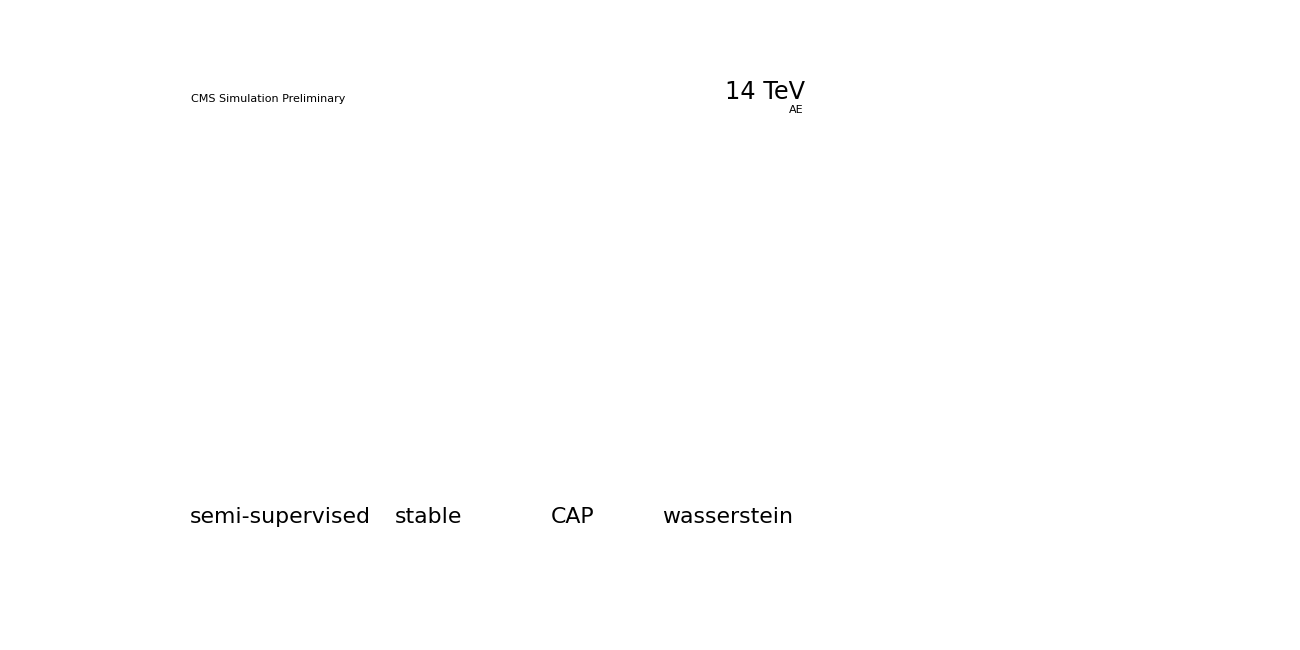

effs/ae_250Hz.svg

effs/ae_250Hz.pdf

effs/ae_250Hz.jpeg

```mathematica
(*Data AE @ 250Hz*)
semisupervised={0.31,0.53,0.00,0.17,1.79,1.05,0.96,17.05,17.50,21.16,1.92,0.06,16.86,15.76,15.65,7.14,0.59,0.33,0.58,17.41};
CAP={0.18,0.44,0.00,0.05,0.98,0.87,0.98,13.67,14.24,18.44,0.82,0.04,14.97,13.93,12.62,3.82,0.36,0.41,1.18,16.67};
stable={2.97,0.39,0.00,0.14,0.81,0.67,0.72,9.52,9.81,14.43,0.62,0.04,12.24,9.46,8.23,2.84,0.29,0.30,0.48,11.91};
wasserstein={0.16,0.22,0.00,0.03,0.77,0.57,0.66,5.38,5.42,14.82,0.51,0.02,12.21,5.47,5.32,2.45,0.20,0.18,0.33,9.64};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: AE @ q99

```mathematica
(*Physics efficiencies@q99—AE architecture*)
semisupervised={0.4288,0.2950,0.0179,0.2803,0.7093,0.6294,0.6411,0.9741,0.9781,0.8964,0.8117,0.1664,0.7294,0.9556,0.9639,0.8772,0.3859,0.7433,0.8560,0.9920}*100;
CAP={0.3915,0.1796,0.0245,0.2493,0.6318,0.6075,0.6276,0.9766,0.9799,0.8929,0.8069,0.1557,0.7204,0.9650,0.9650,0.8607,0.3132,0.6921,0.8174,0.9922}*100;
stable={0.4202,0.2564,0.0186,0.2551,0.7209,0.6716,0.6969,0.9768,0.9808,0.9125,0.8501,0.1741,0.7534,0.9632,0.9652,0.8775,0.3847,0.7525,0.8608,0.9948}*100;
wasserstein={0.3612,0.1392,0.0205,0.2949,0.5833,0.5612,0.5911,0.9690,0.9738,0.8585,0.7207,0.1380,0.6773,0.9552,0.9543,0.8177,0.2628,0.6596,0.7885,0.9781}*100;

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/ae_q99.svg

effs/ae_q99.pdf

effs/ae_q99.jpeg

## Efficiency Plot: VAE @ 250 Hz

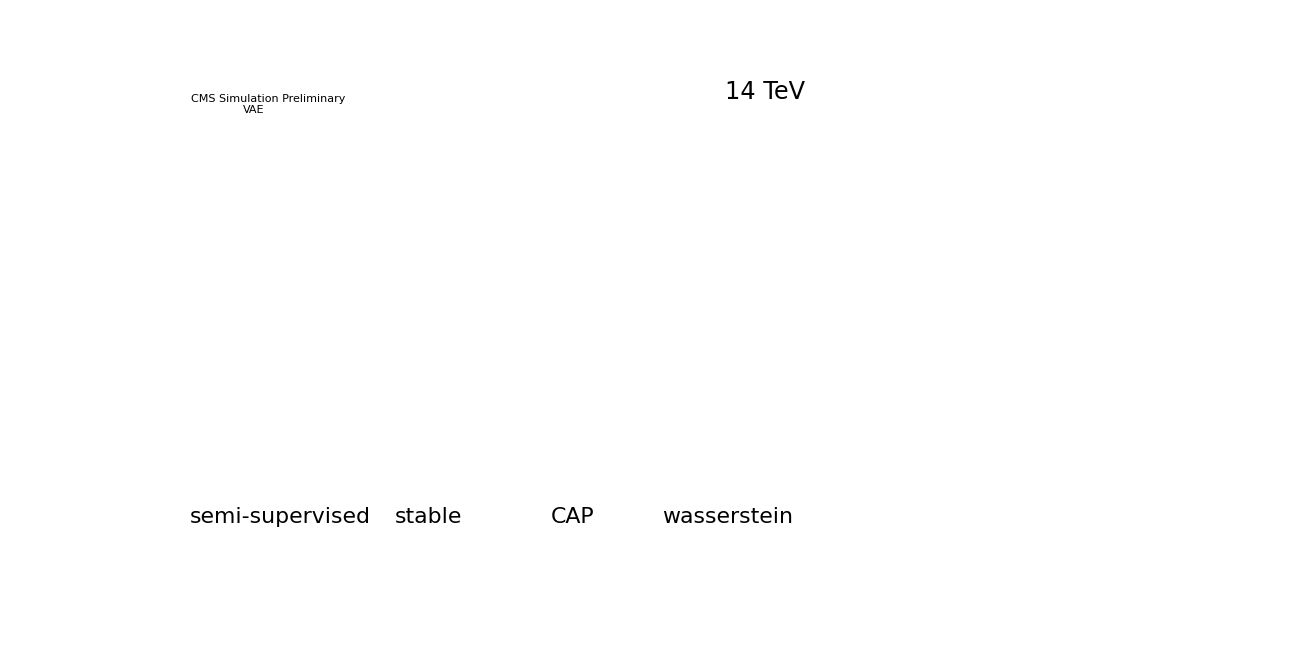

effs/vae_250Hz.svg

effs/vae_250Hz.pdf

effs/vae_250Hz.jpeg

```mathematica
(*Data VAE*)
semisupervised={0.02,0.18,0.00,0.00,0.77,0.86,1.02,8.43,8.88,18.93,0.68,0.04,12.44,10.11,9.15,2.79,0.32,0.24,0.38,15.93};
CAP={0.02,0.20,0.00,0.00,0.82,0.93,1.10,8.87,9.35,19.74,0.73,0.04,12.93,10.70,9.60,2.93,0.32,0.24,0.40,16.83};
stable={0.02,0.19,0.00,0.01,0.95,1.03,1.15,6.34,6.56,21.12,0.65,0.04,15.36,8.08,7.14,2.34,0.33,0.21,0.36,15.90};
wasserstein={0.02,0.21,0.00,0.01,0.91,1.07,1.17,5.77,5.92,23.70,0.78,0.04,15.10,7.62,6.77,2.76,0.32,0.12,0.18,17.37};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"VAE", {0.151, 0.899}]
Export["effs/" <> "vae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_250Hz" <>".jpeg",plot,"JPEG"]
```

```mathematica
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
```

## Efficiency Plot: VAE @ q99

```mathematica
(*Physics efficiencies@q99—VAE architecture*)
semisupervised={0.5297,0.2983,0.0113,0.3704,0.7787,0.6888,0.7295,0.9927,0.9940,0.9333,0.9135,0.2473,0.8001,0.9887,0.9892,0.9489,0.5558,0.8509,0.9209,0.9982}*100;
CAP={0.5120,0.2965,0.0142,0.2861,0.8022,0.7293,0.7638,0.9962,0.9970,0.9401,0.9230,0.3104,0.8148,0.9942,0.9943,0.9644,0.5854,0.8576,0.9250,0.9977}*100;
stable={0.2853,0.1295,0.0094,0.0431,0.6647,0.5822,0.6285,0.9664,0.9697,0.9161,0.8813,0.1855,0.7663,0.9629,0.9704,0.9042,0.4293,0.7982,0.8857,0.9947}*100;
wasserstein={0.3207,0.1391,0.0110,0.0554,0.6634,0.5847,0.6283,0.9864,0.9881,0.9165,0.8816,0.2070,0.7714,0.9823,0.9831,0.9234,0.4569,0.8222,0.8971,0.9945}*100;

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "VAE",{0.151, 0.899}]
Export["effs/" <> "vae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/vae_q99.svg

effs/vae_q99.pdf

effs/vae_q99.jpeg

## Efficiency Plot: DS AE @ 250 Hz

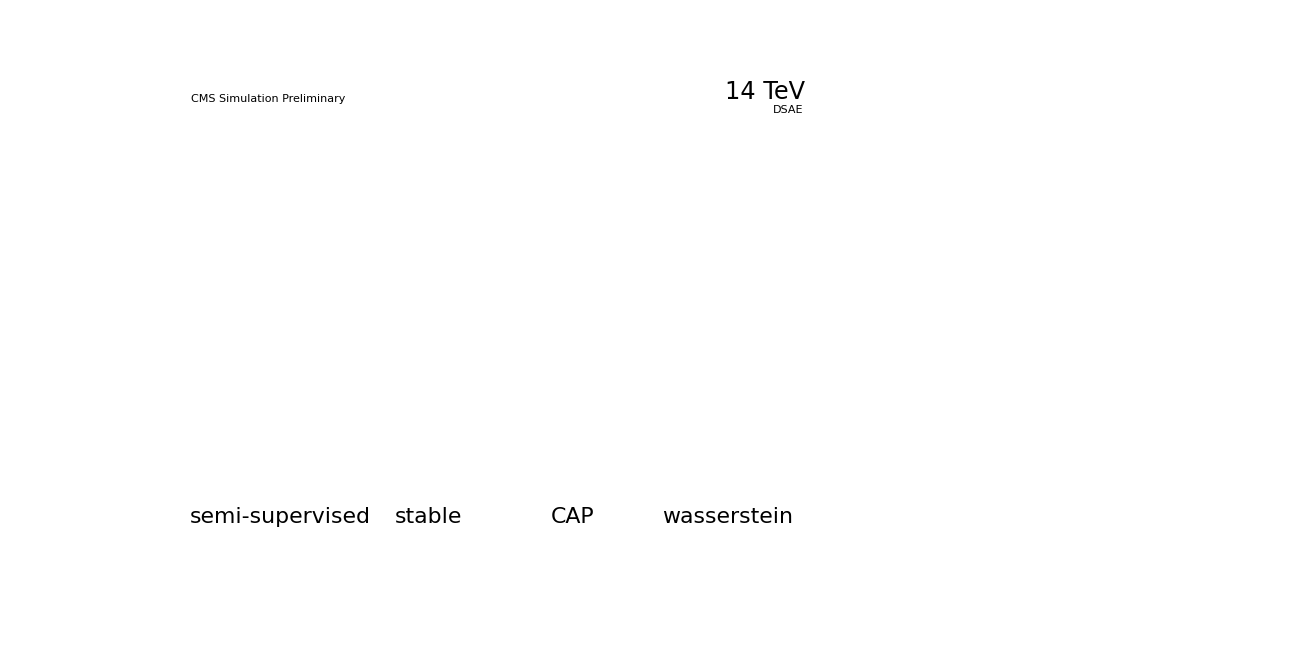

effs/dsae_250Hz.svg

effs/dsae_250Hz.pdf

effs/dsae_250Hz.jpeg

```mathematica
(*Data DS AE*)
semisupervised={0.47,0.59,0.00,0.10,1.22,1.04,1.16,24.23,25.34,17.00,1.16,0.05,13.27,21.69,21.13,6.43,0.40,0.60,1.00,19.04};
CAP={0.39,0.61,0.00,0.10,1.23,1.08,1.20,26.20,26.86,20.58,1.12,0.05,15.23,23.61,23.15,6.91,0.43,0.68,1.12,20.36};
stable={1.01,0.33,0.00,0.04,0.86,0.56,0.68,6.52,6.58,14.04,0.60,0.02,11.11,5.88,6.23,2.13,0.26,0.73,4.65,9.09};
wasserstein={0.15,1.74,0.00,0.02,1.04,0.72,0.84,6.25,6.60,15.32,0.66,0.03,12.84,6.37,6.33,2.67,0.31,0.47,1.36,11.24};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSAE", {0.639, 0.899}]
Export["effs/" <> "dsae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "dsae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsae_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: DS AE @ q99

```mathematica
(*Data DS AE*)
semisupervised={39.85,33.24,1.66,29.69,69.31,61.43,64.87,98.20,98.52,90.27,84.07,15.58,73.85,97.01,97.35,89.51,38.35,75.79,86.89,99.59};
CAP={32.00,13.64,2.12,19.83,56.61,51.48,54.60,95.83,96.38,85.91,73.04,10.89,67.00,93.80,94.04,79.84,24.74,57.40,73.84,98.15};
stable={34.29,12.32,1.99,21.52,54.37,49.06,51.85,96.70,97.19,85.84,73.32,10.52,67.07,94.97,95.06,80.25,23.81,64.76,77.33,98.33};
wasserstein={35.19,15.12,1.70,23.24,56.07,49.45,52.75,96.41,96.94,87.46,77.44,10.62,69.12,94.64,94.82,80.69,26.15,66.53,79.65,98.80};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSAE", {0.639, 0.899}]
Export["effs/" <> "dsae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "dsae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/dsae_q99.svg

effs/dsae_q99.pdf

effs/dsae_q99.jpeg

## Efficiency plot: DS VAE @ 250 Hz

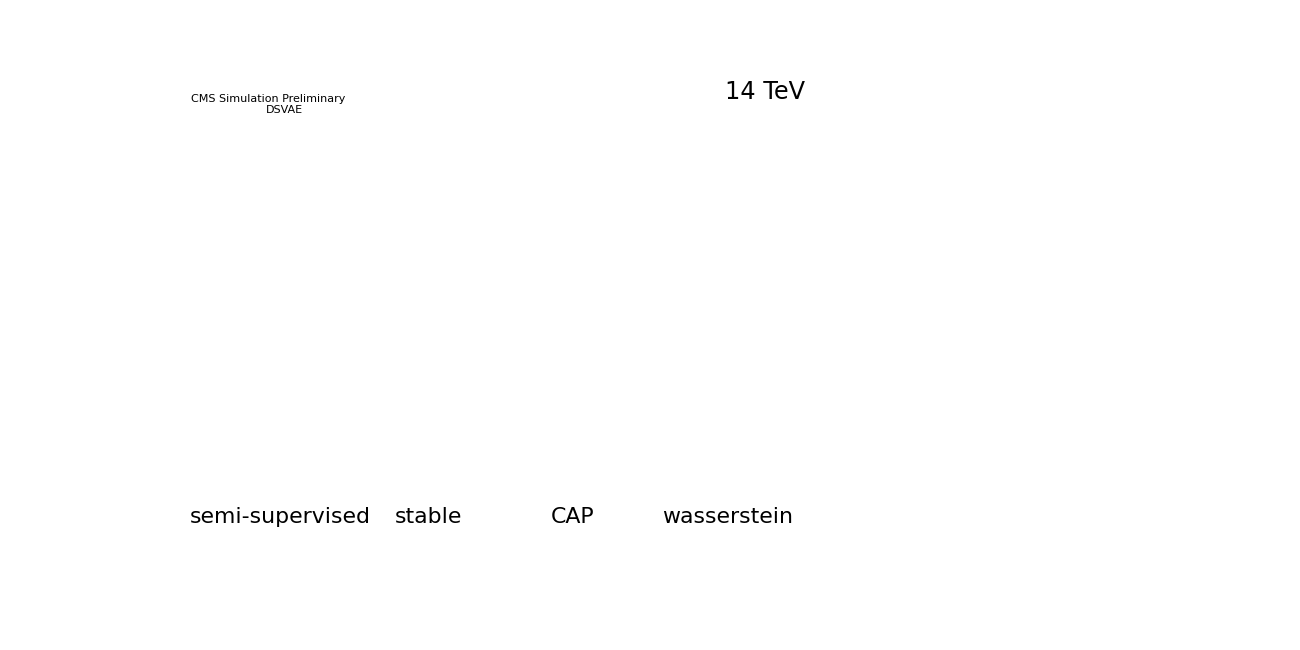

effs/dsvae_250Hz.svg

effs/dsvae_250Hz.pdf

effs/dsvae_250Hz.jpeg

```mathematica
(*Data DS VAE*)
semisupervised={0.11,0.18,0.00,0.01,1.18,0.97,1.12,12.13,12.89,17.85,0.77,0.04,14.00,13.12,11.79,3.63,0.38,0.44,0.76,16.27};
CAP={0.02,0.19,0.00,0.01,1.10,1.02,1.15,9.51,10.00,19.45,0.70,0.04,15.23,11.09,9.72,3.16,0.37,0.27,0.46,16.87};
stable={0.01,0.55,0.00,0.01,0.77,1.02,1.18,9.01,9.50,20.08,0.88,0.04,13.04,11.17,9.46,2.67,0.28,0.21,0.35,16.81};
wasserstein={0.05,0.33,0.00,0.01,0.31,0.15,0.13,1.40,1.53,3.99,0.32,0.02,2.41,0.91,1.21,1.28,0.11,0.03,0.05,1.85};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSVAE", {0.186, 0.899}]
Export["effs/" <> "dsvae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "dsvae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsvae_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: DSVAE @ q99

```mathematica
(*Data DS VAE*)
semisupervised={54.88,30.67,1.47,43.45,79.62,73.19,77.08,99.58,99.65,94.27,92.70,30.04,81.86,99.37,99.36,96.15,58.67,85.27,92.34,99.81};
CAP={55.71,30.01,1.37,38.88,80.55,73.49,77.67,99.42,99.53,94.15,92.66,27.94,81.29,99.13,99.18,95.76,59.44,87.15,93.29,99.84};
stable={38.46,34.41,1.51,44.53,56.00,52.41,49.99,97.32,97.43,89.88,84.81,26.61,74.31,96.91,96.94,88.38,37.00,36.53,62.19,98.82};
wasserstein={34.39,23.17,1.09,10.98,51.54,43.86,42.55,89.02,88.64,86.88,77.23,11.85,68.69,88.09,89.38,77.90,28.50,56.26,76.71,97.38};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSVAE", {0.186, 0.899}]
Export["effs/" <> "dsvae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "dsvae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsvae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/dsvae_q99.svg

effs/dsvae_q99.pdf

effs/dsvae_q99.jpeg

## Efficiency Plot: SVDD @ 250 Hz

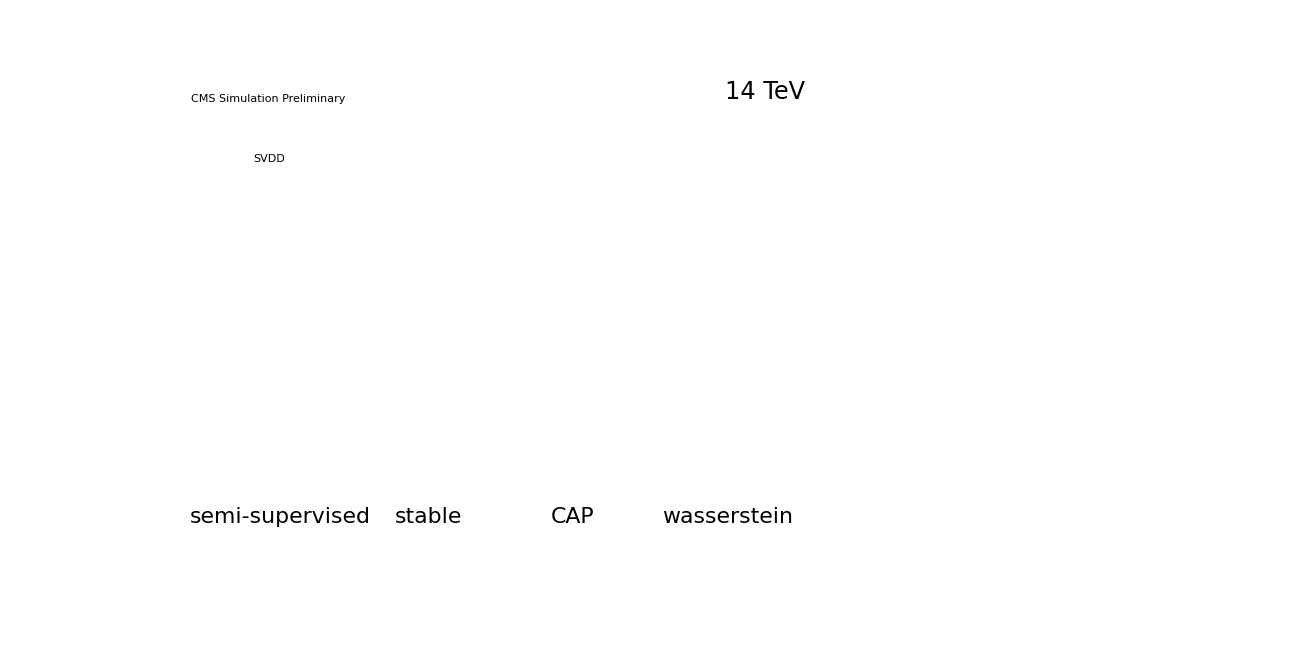

effs/svdd_250Hz.svg

effs/svdd_250Hz.pdf

effs/svdd_250Hz.jpeg

```mathematica
(*Data SVDD*)
semisupervised={0.44,0.14,0.00,1.01,0.90,0.72,0.78,5.23,4.75,16.16,0.67,0.04,11.13,5.35,5.70,2.29,0.24,0.24,0.65,9.50};
CAP={1.14,0.19,0.00,0.05,0.71,0.68,0.81,9.06,9.21,13.26,0.83,0.03,10.59,8.88,8.48,2.99,0.27,0.44,0.72,12.24};
stable={0.50,0.19,0.01,0.11,1.09,0.69,0.58,8.81,8.89,8.40,1.93,0.05,8.41,7.73,7.50,6.27,0.37,0.05,0.06,9.61};
wasserstein={0.71,0.09,0.00,0.03,0.55,0.46,0.58,7.57,7.98,13.30,0.38,0.02,9.92,6.44,6.05,1.91,0.20,0.09,0.14,8.63};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"SVDD", {0.170, 0.81}]
Export["effs/" <> "svdd_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "svdd_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "svdd_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: SVDD @ q99

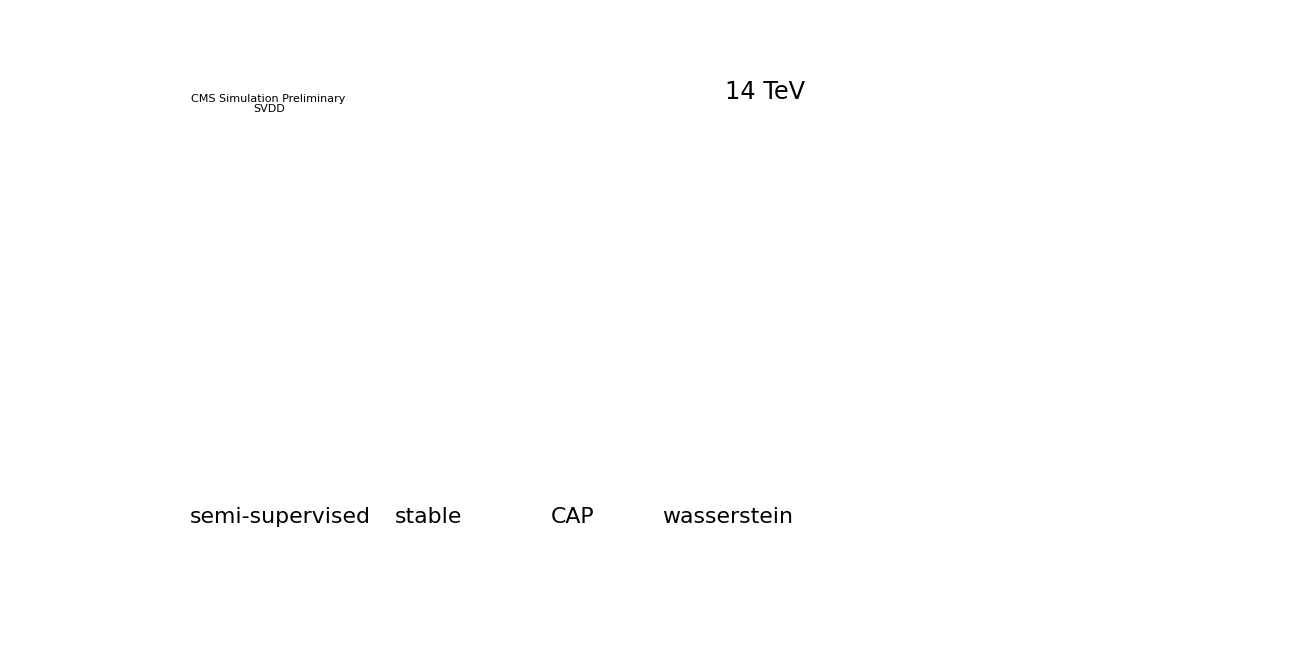

effs/svdd_q99.svg

effs/svdd_q99.pdf

effs/svdd_q99.jpeg

```mathematica
(*Data SVDD*)
semisupervised={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.};
CAP={0.3114,0.0799,0.0114,0.0504,0.5828,0.5171,0.5504,0.9746,0.9775,0.8959,0.8423,0.1431,0.7329,0.9681,0.9703,0.8795,0.3281,0.7376,0.8411,0.9940}*100;
stable={0.4372,0.1603,0.0199,0.1761,0.6725,0.6134,0.6632,0.9599,0.9642,0.9101,0.8648,0.1904,0.7583,0.9529,0.9521,0.8691,0.4413,0.8172,0.8996,0.9944}*100;
wasserstein={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"SVDD", {0.170, 0.90}]
Export["effs/" <> "svdd_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "svdd_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "svdd_q99" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: RealNVP @ 250 Hz

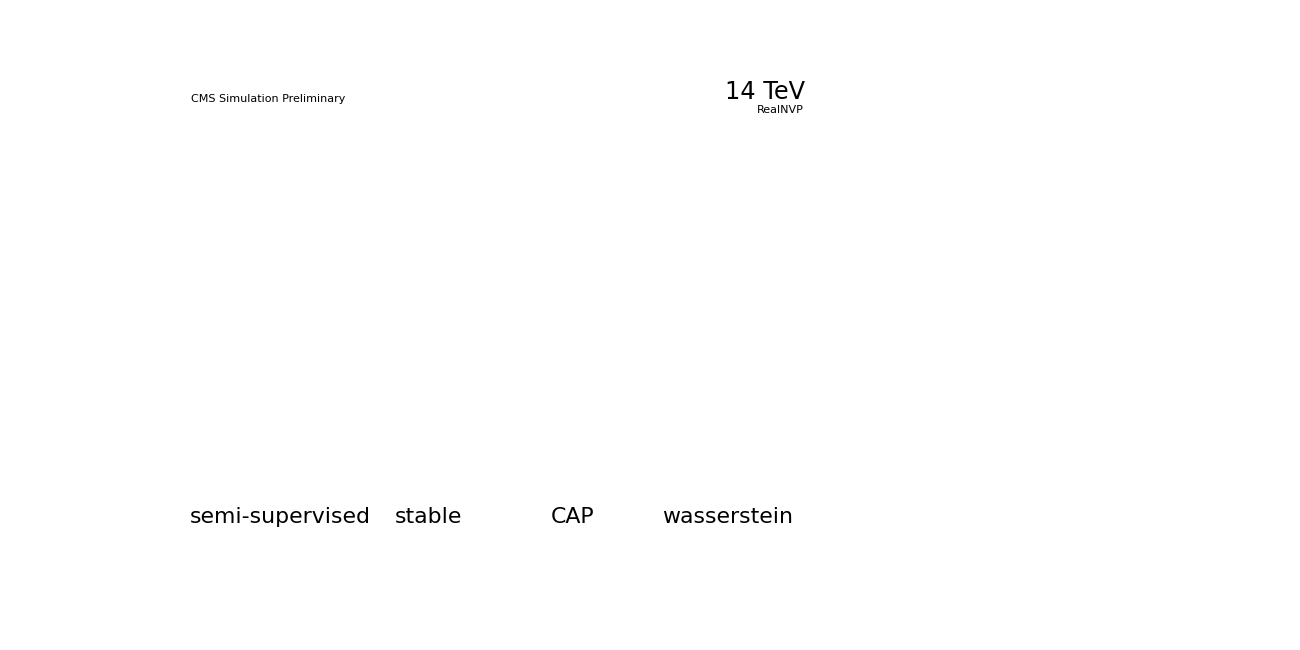

effs/realnvp_250Hz.svg

effs/realnvp_250Hz.pdf

effs/realnvp_250Hz.jpeg

```mathematica
(*Data RealNVP*)
semisupervised={1.13,0.15,0.02,0.20,1.07,0.77,0.90,11.70,12.06,13.67,0.93,0.07,10.29,10.45,10.66,3.46,0.41,1.95,9.18,11.67};
CAP={2.55,0.04,0.00,0.71,0.49,0.31,0.28,12.71,12.80,3.98,0.61,0.06,3.86,9.81,8.85,2.87,0.19,0.16,0.39,4.59};
stable={1.47,0.04,0.00,0.17,0.34,0.36,0.37,12.19,12.77,3.79,0.54,0.04,4.60,9.92,8.83,2.26,0.14,0.15,0.23,5.09};
wasserstein={0.99,0.02,0.00,0.58,0.18,0.19,0.21,6.25,6.29,1.99,0.25,0.04,2.19,5.28,4.72,1.15,0.13,0.08,0.16,2.50};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"RealNVP", {0.639, 0.899}]
Export["effs/" <> "realnvp_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "realnvp_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "realnvp_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: RealNVP @ q99

```mathematica
(*Physics efficiencies@q99—RealNVP architecture*)
semisupervised={0.5609,0.1869,0.0170,0.4878,0.8125,0.7674,0.7952,0.9964,0.9969,0.9413,0.9236,0.2738,0.8096,0.9937,0.9932,0.9563,0.5318,0.8301,0.9176,0.9981}*100;
CAP={0.1569,0.0093,0.0295,0.2013,0.2650,0.2759,0.2741,0.8825,0.8859,0.4385,0.2729,0.1219,0.3505,0.8307,0.8214,0.5658,0.1534,0.1989,0.2628,0.5732}*100;
stable={0.2054,0.0087,0.0243,0.2364,0.2386,0.2378,0.2293,0.8505,0.8516,0.4103,0.2509,0.1107,0.3336,0.7836,0.7800,0.5298,0.1430,0.2298,0.3402,0.5236}*100;
wasserstein={0.1788,0.0134,0.0193,0.2386,0.2034,0.2150,0.2052,0.8552,0.8573,0.3947,0.2339,0.0991,0.3217,0.7978,0.7859,0.5193,0.1224,0.1557,0.1899,0.5227}*100;

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"RealNVP", {0.639, 0.899}]
Export["effs/" <> "realnvp_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "realnvp_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "realnvp_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/realnvp_q99.svg

effs/realnvp_q99.pdf

effs/realnvp_q99.jpeg

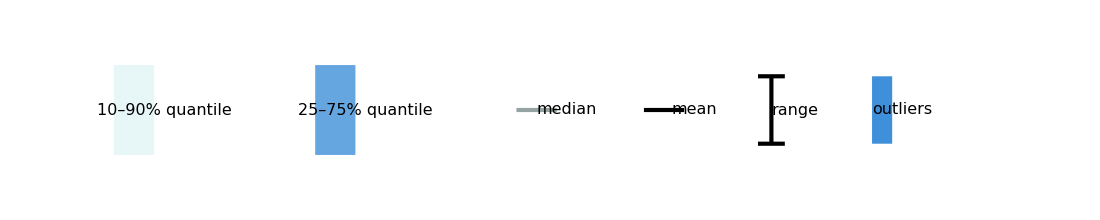

effs/legend.pdf

```mathematica
legendOnly=Graphics[{{EdgeForm[None],FaceForm[Directive[RGBColor["#92dadd"],Opacity[0.22]]],Rectangle[{0,0},{0.6,0.4}]},Text[Style["10–90% quantile",FontFamily->"TeX Gyre Heros",16],{0.75,0.2},{-1,0}],{EdgeForm[None],FaceForm[Directive[RGBColor["#3f90da"],Opacity[0.8]]],Rectangle[{3.0,0},{3.6,0.4}]},Text[Style["25–75% quantile",FontFamily->"TeX Gyre Heros",16],{3.75,0.2},{-1,0}],{Directive[RGBColor["#94a4a2"],AbsoluteThickness[3]],Line[{{6.0,0.2},{6.6,0.2}}]},Text[Style["median",FontFamily->"TeX Gyre Heros",16],{6.75,0.2},{-1,0}],{Directive[Black,AbsoluteThickness[3]],Line[{{7.9,0.2},{8.5,0.2}}]},Text[Style["mean",FontFamily->"TeX Gyre Heros",16],{8.65,0.2},{-1,0}],{Directive[Black,AbsoluteThickness[3]],Line[{{9.8,0.05},{9.8,0.35}}],Line[{{9.6,0.05},{10.0,0.05}}],Line[{{9.6,0.35},{10.0,0.35}}]},Text[Style["range",FontFamily->"TeX Gyre Heros",16],{10.15,0.2},{-1,0}],{RGBColor["#3f90da"],Rectangle[{11.3,0.05},{11.6,0.35}]},Text[Style["outliers",FontFamily->"TeX Gyre Heros",16],{11.75,0.2},{-1,0}]},PlotRange->{{-0.2,13.2},{-0.2,0.6}},ImageSize->1100,Background->White]

Export["effs/" <> "legend" <>".pdf",legendOnly,"PDF"]
```